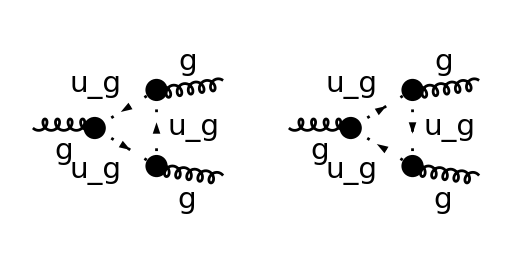
Hi, Vladyslave and  Rolf:
Thank you very much for your answers. But the problem is not resolved.The reason is as follows:

Your conventions of the Feynman diagrams etc. are slightly different from mine.But this is not important because they lead to the same (incorrect) result after using FeynCalc to carry out OneLoop with the.nb file you sent me in the email.

  I employed the 2 amplitudes you obtained below  two Feynman diagrams  and just above  amps[[2]]/.p3→-p2/.p2→p.  I am interested only in the logarithmically divergent terms,i.e.  the coefficient of the function B0(p^2,0,0).  The result contains the terms of the form:
-(p̄)^2 (p̄)^ν (ḡ)^λμ+(p̄)^2 (p̄)^λ (ḡ)^μν-(p̄)^2 (p̄)^μ (ḡ)^λν.
The correct form should be
-(p̄)^2 (p̄)^ν (ḡ)^λμ+2(p̄)^2 (p̄)^λ (ḡ)^μν-(p̄)^2 (p̄)^μ (ḡ)^λν,
which is formally consistent with that  you defined in
	PTVertexFuLorentzStruct[{p_,q_,k_},{mu_,nu_,si_},{a_,b_,c_}]:=
-I SUNF[a,b,c](MTD[mu,nu]FVD[p-q,si]+MTD[nu,si]FVD[q-k,mu]+MTD[si,mu]FVD[k-p,nu])


My result is attached in this email for your reference. 
My question is: Why it does not produce the expected (Lorentz) tensor structure? My hand-calculation and the calculation of Politzer
did produce the correct structure, as expected.  Could you please use FeynCalc to check the consistce?
Five or six years ago   I and a student    used FeynCalc to calculate the graviton self-energy  in a new theory called 'quantum Yang-Mills gravity' that I formulated.  I do not remember such inconsistence in the loop calculations.   At that time we used Mathematica 8.  Is it possible that now Mathematica has evolved to version 11 which may not  be completely consistent with FeynCalc?           JP




-Graphics-

{(ⅈ C_A g_s^3 q^μ (q-p2)^ν f^abc (-p2-p3+q)^λ)/(2 q^2.(q-p2)^2.(-p2-p3+q)^2),(ⅈ C_A g_s^3 q^λ (p2-q)^μ f^abc (p2+p3-q)^ν)/(2 q^2.(q-p2)^2.(-p2-p3+q)^2)}

```mathematica
amps[[2]]/.p3->-p2/.p2->p
```